# Approximation in Policy Space for Betting on a Coin

## Supplemental material for Sec. 5.9.2.

```mathematica
importDirectory=ParentDirectory[NotebookDirectory[]]<>"/files/coin";
```

```mathematica
SetDirectory@importDirectory
```

```mathematica
FileNames[]
```

{approximatePolicy.csv,exactPolicy.csv,parameters.txt}

```mathematica
Import["parameters.txt"]
```

max number of coins: 100
probability of heads: 0.75

```mathematica
maxNumberOfCoins=100;
p=0.75;
```

```mathematica
exactPolicy=Flatten@Import["exactPolicy.csv"];
```

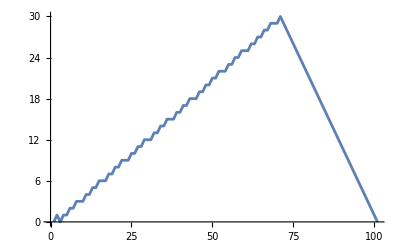

```mathematica
ListLinePlot[exactPolicy]
```

```mathematica
approximatePolicy=Flatten@Import["approximatePolicy.csv"];
```

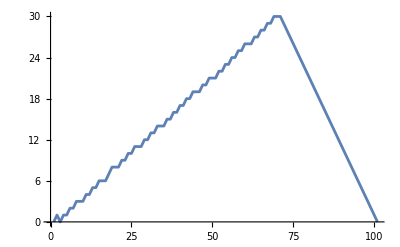

```mathematica
ListLinePlot[approximatePolicy]
```

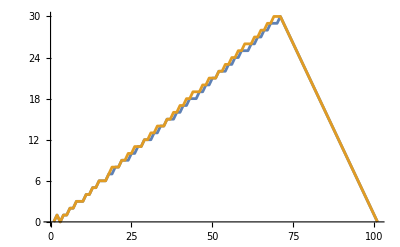

```mathematica
ListLinePlot[{exactPolicy,approximatePolicy},PlotRange->All]
```

```mathematica
Table[(2p-1)x,{x,0,maxNumberOfCoins}]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.5,34.,34.5,35.,35.5,36.,36.5,37.,37.5,38.,38.5,39.,39.5,40.,40.5,41.,41.5,42.,42.5,43.,43.5,44.,44.5,45.,45.5,46.,46.5,47.,47.5,48.,48.5,49.,49.5,50.}

```mathematica
ε=10^-4;
```

```mathematica
SetPrecision[#,4]&/@Table[NMaximize[{p Log[x+y+ε]+(1-p)Log[x-y+ε],0<=y<=Min[x,maxNumberOfCoins-x]},y],{x,0,maxNumberOfCoins}];
```

```mathematica
logPolicy=SetPrecision[#,4]&/@Table[NArgMax[{p Log[x+y+ε]+(1-p)Log[x-y+ε],0<=y<=Min[x,maxNumberOfCoins-x]},y],{x,0,maxNumberOfCoins}]
```

{0,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.,32.,31.,30.,29.,28.,27.,26.,25.,24.,23.,22.,21.,20.,19.,18.,17.,16.,15.,14.,13.,12.,11.,10.,9.,8.,7.,6.,5.,4.,3.,2.,1.,-0.00008647}

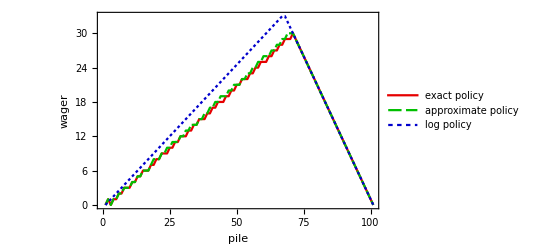

```mathematica
plot=ListLinePlot[{exactPolicy,approximatePolicy,logPolicy},
PlotRange->All,
PlotLegends->{"exact policy","approximate policy","log policy"},
PlotTheme->"Monochrome",
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,12],
FrameLabel->{Style["pile",FontSize->12],Style["wager",FontSize->12]},
PlotMarkers->None,
PlotStyle->{
RGBColor[0.9,0,0],
RGBColor[0,0.75,0],
RGBColor[0,0,0.8]
}]
```

```mathematica
exportDirectory=NotebookDirectory[]<>"/output/coin";
```

```mathematica
SetDirectory@exportDirectory
```

```mathematica
Export["approximationInPolicySpace.pdf",plot]
```

approximationInPolicySpace.pdf